```mathematica
Simplify[Integrate[b/a*Tan[a*b*Divide[x,Power[a,2]+Power[b,2]]],{x,0,1}], {a>0, b>0}]
```

-((a^2+b^2) Log[Cos[(a b)/(a^2+b^2)]])/a^2

```mathematica
Simplify[Integrate[Tan[Divide[x,e+Divide[1,e]]],{x,0,1}], {e>0}]
```

-((1+e^2) Log[Cos[e/(1+e^2)]])/e

```mathematica
Simplify[Integrate[ArcTan[1/e*Tan[Divide[x,e+Divide[1,e]]]],{x,0,1}], {e>0}]
```

18.4349

26.2031

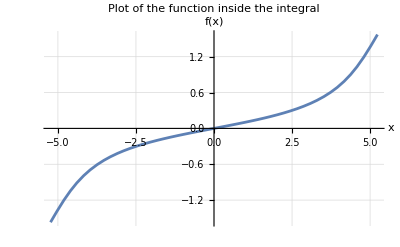

```mathematica
(*Set semiaxes and shar rate*)
a=3.0;
b = 1.0;
γ = 1;
ω = (a*b*γ)/(a^2+b^2);
f[x_]:=ArcTan[b/a*Tan[ω*x]]
angle = ArcTan[b/a]*180/Pi
(2*ω)/Pi NIntegrate[f[x],{x, 0, Pi/(2*ω)} ]*180/Pi
Plot[f[x],{x,-Pi/(2*ω),Pi/(2*ω)},PlotRange->All,PlotLabel->"Plot of the function inside the integral",AxesLabel->{"x","f(x)"},GridLines->Automatic]
```

```mathematica
ϕ[t_] = ArcTan[λ*Tan[ω*t]];
der[t_]=D[ϕ[t], t]
Abs[der[t]]
```

(λ ω Sec[t ω]^2)/(1+λ^2 Tan[t ω]^2)

Abs[(λ ω Sec[t ω]^2)/(1+λ^2 Tan[t ω]^2)]

```mathematica
β = (α^2-1)/(α^2+1);
f[ϕ_] :=γ/2*(1-β*Cos[2*ϕ]);
diff= α;
ϵ = diff/γ;
```

2.1504

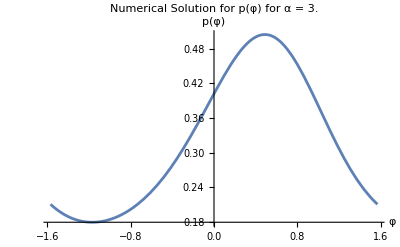

```mathematica
(*First,define the necessary functions and parameters as you did before*)γ=1;
β[α_]:=(α^2-1)/(α^2+1);
f[φ_,α_]:=-γ/2 (1-β[α] Cos[2 φ]);
ε[α_]:=α/10;
c[α_]:=1 (*(γ*α)/(Pi*(α^2+1))*);

(*Define the solver function for a specific alpha value*)
solveForAlpha[alphaValue_]:=NDSolveValue[{p'[φ]==f[φ,alphaValue]*p[φ]/ε[alphaValue]+c[alphaValue],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}];

(*Solve for a specific alpha value*)
αValue=3.0;
solution=solveForAlpha[αValue];

(*Integrate the solution to enforce normalization*)
integralValue=NIntegrate[solution[φ],{φ,-π/2,π/2}];

(*Normalize the solution if needed*)
normalizedSolution[φ_]:=solution[φ]/integralValue;

integralValue
Plot[normalizedSolution[φ],{φ,-π/2,π/2},AxesLabel->{"φ","p(φ)"},PlotLabel->"Numerical Solution for p(φ) for α = "<>ToString[αValue],PlotRange->All]
```

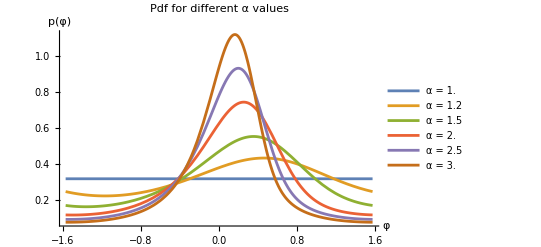

```mathematica
(*Parameters and functions definitions*)
γ=1.0;
β[α_]:=(α^2-1)/(α^2+1);
f[φ_,α_]:=-γ/2* (1.0-β[α]^0.4 Cos[2 φ]) (*-2*ArcTan[1/α]]);*)
(*ε[α_]:= 2/3*(α^4-1)/α*((2*α^2-1)/Sqrt[α^2-1]*Log[α+Sqrt[α^2-1]])^-1*)(*Perrin*) 
(*ε[α_]:=0.1/Log[2*α-1/3]/γ;*)
noise = .5;
ε[α_, φ_]:=noise*α^-3;
c=1;  (*Constant for this example*)

(*Define the solver function for a specific alpha value*)
solveForAlpha[alphaValue_]:=NDSolveValue[{p'[φ]==(f[φ,alphaValue]*p[φ]+c)/ε[alphaValue, φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}];

(*Define the range of alpha values*)
alphaValues={1.0, 1.2,1.5, 2.0,2.5, 3.0 }; (*Change values as needed*)
(* alphaValues={1.2}; Change values as needed*)
(*Solve and normalize solutions for each alpha,storing results*)
solutions=Table[Module[{solution,integralValue,normalizedSolution},solution=solveForAlpha[alpha];
integralValue=NIntegrate[solution[φ],{φ,-π/2,π/2}];
normalizedSolution=solution[φ]/integralValue;
{alpha,normalizedSolution}],{alpha,alphaValues}];

(*Plot each normalized solution as a function of φ*)
Plot[Evaluate[
Table[solutions[[i,2]],{i,
Length[solutions]}]],{φ,-π/2,π/2},
PlotLegends->
Placed[Table[
"α = "<>ToString[solutions[[i,1]]],{i,
Length[solutions]}],Above],
AxesLabel->{"φ","p(φ)"},
PlotLabel->"Pdf for different α values",
PlotRange->{{-Pi/2,Pi/2},{0,All}}]
```

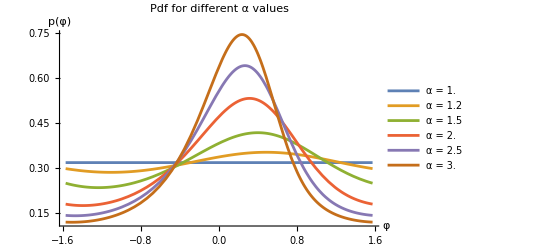

```mathematica
(*Parameters and functions definitions*)
γ=1.0;
β[α_]:=(α^2-1)/(α^2+1);
f[φ_,α_]:=-γ/2* (1.0-β[α]Sign[Cos[2 φ]]*Sqrt[Abs[Cos[2 φ]]]) (*-2*ArcTan[1/α]]);*)
f[φ_,α_]:=-γ/2* (1.0-β[α]Cos[2 φ]) (*-2*ArcTan[1/α]]);*)
(*ε[α_]:= 2/3*(α^4-1)/α*((2*α^2-1)/Sqrt[α^2-1]*Log[α+Sqrt[α^2-1]])^-1*)(*Perrin*) 
(*ε[α_]:=0.1/Log[2*α-1/3]/γ;*)
noise = 0.5;
ε[α_, φ_]:=noise*Exp[-0.1*α];
ε[α_, φ_] := noise* α^-2

c=1;  (*Constant for this example*)

(*Define the solver function for a specific alpha value*)
solveForAlpha[alphaValue_]:=NDSolveValue[{p'[φ]==(f[φ,alphaValue]*p[φ]+c)/ε[alphaValue, φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}];

(*Define the range of alpha values*)
alphaValues={ 1.0, 1.2,1.5, 2.0,2.5, 3.0}; (*Change values as needed*)
(* alphaValues={1.2}; Change values as needed*)
(*Solve and normalize solutions for each alpha,storing results*)
solutions=Table[Module[{solution,integralValue,normalizedSolution},solution=solveForAlpha[alpha];
integralValue=NIntegrate[solution[φ],{φ,-π/2,π/2}];
normalizedSolution=solution[φ]/integralValue;
{alpha,normalizedSolution}],{alpha,alphaValues}];

(*Plot each normalized solution as a function of φ*)
Plot[Evaluate[
Table[solutions[[i,2]],{i,
Length[solutions]}]],{φ,-π/2,π/2},
PlotLegends->
Placed[Table[
"α = "<>ToString[solutions[[i,1]]],{i,
Length[solutions]}],Above],
AxesLabel->{"φ","p(φ)"},
PlotLabel->"Pdf for different α values",
PlotRange->{{-Pi/2,Pi/2},{0,All}}]
```

```mathematica
γ=1.0;
β[α_]:=(α^2-1)/(α^2+1);
f[φ_,α_]:=-γ/2* (1.0-β[α]Cos[2 φ]) (*-2*ArcTan[1/α]]);*)
ε[α_]:= 2/3*(α^4-1)/α*((2*α^2-1)/Sqrt[α^2-1]*Log[α+Sqrt[α^2-1]])^-1(*Perrin*) 
ε[α_]:= Log[α]/α^3 
(*ε[α_]:=0.1/Log[2*α-1/3]/γ;*)
noise = 0.2;
(*ε[α_, φ_]:=noise*α^-2;*)
c=1;  (*Constant for this example*)

(*Define the solver function for a specific alpha value*)
solveForAlpha[alphaValue_]:=NDSolveValue[{p'[φ]==(f[φ,alphaValue]*p[φ]+c)/ε[alphaValue, φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}];

(*Define the range of alpha values*)
alphaValues={ 1.2,1.5, 2.0,2.5, 3.0}; (*Change values as needed*)
(* alphaValues={1.2}; Change values as needed*)
(*Solve and normalize solutions for each alpha,storing results*)
solutions=Table[Module[{solution,integralValue,normalizedSolution},solution=solveForAlpha[alpha];
integralValue=NIntegrate[solution[φ],{φ,-π/2,π/2}];
normalizedSolution=solution[φ]/integralValue;
{alpha,normalizedSolution}],{alpha,alphaValues}];

(*Plot each normalized solution as a function of φ*)
Plot[Evaluate[
Table[solutions[[i,2]],{i,
Length[solutions]}]],{φ,-π/2,π/2},
PlotLegends->
Placed[Table[
"α = "<>ToString[solutions[[i,1]]],{i,
Length[solutions]}],Above],
AxesLabel->{"φ","p(φ)"},
PlotLabel->"Pdf for different α values",
PlotRange->{{-Pi/2,Pi/2},{0,All}}]
```

NDSolveValue::underdet: There are more dependent variables, {p[φ],ε[1.2,φ]}, than equations, so the system is underdetermined.

NDSolveValue::dsvar: -φ cannot be used as a variable.

NIntegrate::inumr: The integrand NDSolveValue[{p'[φ]==(1-0.5 (1.+Times[«2»]) p[φ])/ε[1.2,φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}][φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5708,1.5708}}.

NDSolveValue::underdet: There are more dependent variables, {p[φ],ε[1.2,φ]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolveValue::underdet will be suppressed during this calculation.

NDSolveValue::dsvar: -φ cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NIntegrate::inumr: The integrand NDSolveValue[{p'[φ]==(1-0.5 (1.+Times[«2»]) p[φ])/ε[1.2,φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}][φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5708,1.5708}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NDSolveValue::underdet: There are more dependent variables, {p[φ],ε[1.2,φ]}, than equations, so the system is underdetermined.

NDSolveValue::dsvar: -φ cannot be used as a variable.

NIntegrate::inumr: The integrand NDSolveValue[{p'[φ]==(1-0.5 (1.+Times[«2»]) p[φ])/ε[1.2,φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}][φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5708,1.5708}}.

NDSolveValue::underdet: There are more dependent variables, {p[φ],ε[1.2,φ]}, than equations, so the system is underdetermined.

NDSolveValue::underdet: There are more dependent variables, {p[φ],ε[1.5,φ]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolveValue::underdet will be suppressed during this calculation.

NDSolveValue::dsvar: -φ cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

NIntegrate::inumr: The integrand NDSolveValue[{p'[φ]==(1-0.5 (1.+Times[«2»]) p[φ])/ε[1.5,φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}][φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5708,1.5708}}.

NIntegrate::inumr: The integrand NDSolveValue[{p'[φ]==(1-0.5 (1.+Times[«2»]) p[φ])/ε[2.,φ],p[-π/2]==p[π/2]},p,{φ,-π/2,π/2}][φ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1.5708,1.5708}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
ϕ= 1/2 ArcCos[(α^2+1)/(α^2-1)]//FullSimplify
```

1/2 ArcCos[(1+α^2)/(-1+α^2)]